```mathematica
Φ[x_]:=CDF[NormalDistribution[],x]
```

```mathematica
CDF[LogNormalDistribution[δ,β],x]
```

Piecewise[{{1/2 Erfc[(δ-Log[x])/(√2 β)], x>0}, {0, True}}]

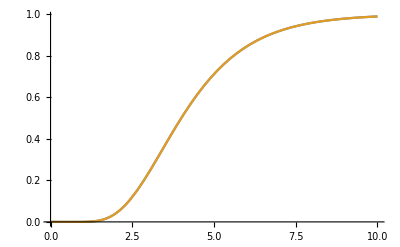

```mathematica
Plot[{CDF[LogNormalDistribution[Log[4],0.4],x], Φ[Log[x/4]/0.4]},{x,0,10}]
```

```mathematica
Φ[Log[x/δ]/β]
```

1/2 Erfc[-Log[x/δ]/(√2 β)]

```mathematica
Solve[1/2 Erfc[-Log[x/δ]/(√2 β)]==y, x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→ⅇ^(-√2 β InverseErfc[2 y]) δ}}

```mathematica
D[Φ[Log[x/δ]/β], x]
```

```mathematica
(ⅇ^(-Log[x/δ]^2/(2 β^2)))/(√(2 π) x β)
```

```mathematica
Erfc[0.50]
```

0.4795

```mathematica
InverseErfc[0.5]
```

0.476936

```mathematica
CDF[NormalDistribution[],x]
```

1/2 Erfc[-x/(√2)]

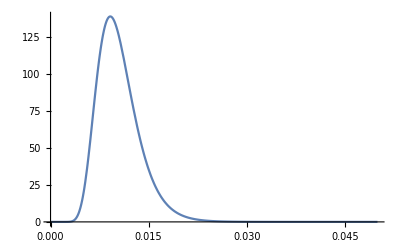

```mathematica
Plot[(ⅇ^(-Log[x/0.01]^2/(2 0.3^2)))/(√(2 π) x 0.3), {x,0, 0.05}]
```